## Creating currency conversion table

```mathematica
str="EUR
EUR
EUR
EUR
EUR
EUR
EUR
EUR
EUR
EUR
EUR
EUR
EUR
EUR
EUR
GTQ
GTQ
MAD
MAD
MAD
MAD
KRW
GBP
GBP
GBP
GBP
GBP
GBP
GBP
GBP
GBP
GBP
GBP
GBP
GBP
GBP
GBP
GBP
USD
USD
USD
USD
USD
USD
USD
USD
USD
USD
USD
USD
USD
USD
USD
USD
USD
VND
VND";
```

```mathematica
curr=Union[StringSplit[str]]
```

{EUR,GBP,GTQ,KRW,MAD,USD,VND}

```mathematica
conversions= AssociationMap[QuantityMagnitude[CurrencyConvert[Quantity[1,#],"EUR"]]&,curr]
```

<|EUR→1,GBP→1.10583,GTQ→0.108524,KRW→0.000750413,MAD→0.0921225,USD→0.84246,VND→0.0000363882|>

```mathematica
Export["/Users/katjad/Documents/Github/CS146/LBA/conversions.json",conversions]
```

/Users/katjad/Documents/Github/CS146/LBA/conversions.json

```mathematica
conversions["KRW"]
```

0.000750413

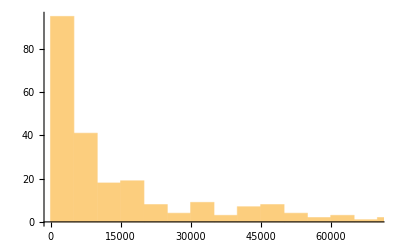

```mathematica
Histogram[Divide@@@DeleteMissing[EntityValue["Country",{"GDP","Population"}],1,2],{5000},PlotRange->{{0,70000},All}]
```

## Getting the GDP for each country

```mathematica
Divide@@@EntityValue[{Entity["Country","Germany"],Entity["Country","Guatemala"],Entity["Country","Morocco"],Entity["Country","SouthKorea"],Entity["Country","UnitedKingdom"],Entity["Country","UnitedStates"],Entity["Country","Vietnam"]},{"GDP","Population"},"EntityAssociation"]
```

<|Germany→46046. $,Guatemala→4363.14 $,Morocco→3255.27 $,South Korea→32061.9 $,United Kingdom→41864.5 $,United States→65116.9 $,Vietnam→2715.28 $|>

```mathematica
Values[QuantityMagnitude[UnitConvert[Divide@@@EntityValue[{Entity["Country","Germany"],Entity["Country","Guatemala"],Entity["Country","Morocco"],Entity["Country","SouthKorea"],Entity["Country","UnitedKingdom"],Entity["Country","UnitedStates"],Entity["Country","Vietnam"]},{"GDP","Population"},"EntityAssociation"],"Euros"/("People"*"Years")]]]
```

{38972.5,3692.88,2755.2,27136.6,35433.3,55113.8,2298.16}

```mathematica
Divide@@@DeleteMissing[EntityValue[{Entity["Country","Germany"],Entity["Country","UnitedKingdom"],Entity["Country","UnitedStates"],Entity["Country","SouthKorea"],Entity["Country","Morocco"],Entity["Country","Vietnam"],Entity["Country","Guatemala"]},{"GDP","Population"},"EntityAssociation"],1,2]
```

<|Germany→46046. $,United Kingdom→41864.5 $,United States→65116.9 $,South Korea→32061.9 $,Morocco→3255.27 $,Vietnam→2715.28 $,Guatemala→4363.14 $|>

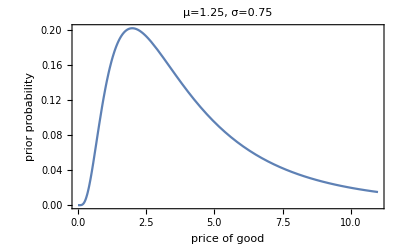

```mathematica
Plot[PDF[LogNormalDistribution[1.25,0.75],x],{x,0,11},Frame->True,FrameLabel->{Style["price of good",Medium],Style["prior probability",Medium]},PlotLabel->"μ=1.25, σ=0.75"]
```

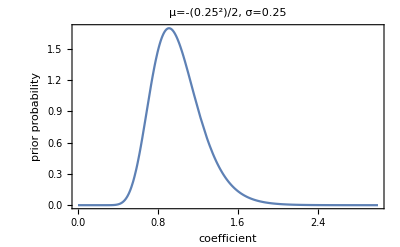

```mathematica
Plot[PDF[LogNormalDistribution[-0.25^2/2,0.25],x],{x,0,3},Frame->True,FrameLabel->{Style["coefficient",Medium],Style["prior probability",Medium]},PlotLabel->"μ=-0.25^2/2, σ=0.25"]
```

```mathematica
Mean[LogNormalDistribution[μ,σ]]
```

ⅇ^(μ+σ^2/2)

```mathematica
Solve[Mean[LogNormalDistribution[μ,σ]]==1,μ,Reals]
```

{{μ→-σ^2/2}}

```mathematica
μ==-σ^2/2
```

```mathematica
Log[1]
```

0